```mathematica
ClearAll["Global`*"]
```

## 3 points

```mathematica
timeInterval={Subscript[t, -2],Subscript[t, -1],Subscript[t, 0]};
coef=Inverse@{
{Subscript[t, -2]^2,Subscript[t, -1]^2,Subscript[t, 0]^2},
{Subscript[t, -2],Subscript[t, -1],Subscript[t, 0]},
{1,1,1}
};
Do[Subscript[η, -i][v_]=FullSimplify[coef[[3-i]].{v^2,v,1}],{i,2,0,-1}]
```

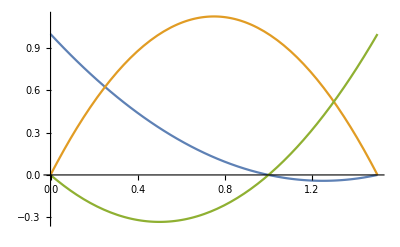

```mathematica
r={Subscript[η, -2][v],Subscript[η, -1][v],Subscript[η, 0][v]}/.{Subscript[t, -2]->0,Subscript[t, -1]->1,Subscript[t, 0]-> 3/2};
Plot[Evaluate@r,{v,0,3/2}]
```

```mathematica
(Subscript[η, -2][.7]+Subscript[η, -1][.7]+Subscript[η, 0][.7])/.{Subscript[t, -2]->0,Subscript[t, -1]->1,Subscript[t, 0]-> 2}
```

1.

```mathematica
Do[
Print[FullSimplify@D[Subscript[η, -i][v], v]/.{v->Subscript[t, 0]}];
Print[FullSimplify@D[Subscript[η, -i][v], v,v]/.{v->Subscript[t, 0]}];
Print[],
{i,2,0,-1}]
```

-(t_-1-t_0)/((t_-2-t_-1) (t_-2-t_0))

2/((t_-2-t_-1) (t_-2-t_0))

(t_-2-t_0)/((t_-2-t_-1) (t_-1-t_0))

2/((t_-2-t_-1) (-t_-1+t_0))

(t_-2+t_-1-2 t_0)/((t_-2-t_0) (-t_-1+t_0))

2/((t_-2-t_0) (t_-1-t_0))

## 4 points

```mathematica
timeInterval={Subscript[t, -3],Subscript[t, -2],Subscript[t, -1],Subscript[t, 0]};
coef=Inverse@{
{Subscript[t, -3]^3,Subscript[t, -2]^3,Subscript[t, -1]^3,Subscript[t, 0]^3},
{Subscript[t, -3]^2,Subscript[t, -2]^2,Subscript[t, -1]^2,Subscript[t, 0]^2},
{Subscript[t, -3],Subscript[t, -2],Subscript[t, -1],Subscript[t, 0]},
{1,1,1,1}
};
Do[Subscript[η, -i][v_]=FullSimplify[coef[[4-i]].{v^3,v^2,v,1}],{i,3,0,-1}]
```

```mathematica
Do[
Print[FullSimplify@D[Subscript[η, -i][v], v]/.{v->Subscript[t, 0]}];
Print[FullSimplify@D[Subscript[η, -i][v], v,v]/.{v->Subscript[t, 0]}];
Print[],
{i,3,0,-1}]
```

(t_-2 (t_-1-t_0)-t_-1 t_0+t_0^2)/((t_-3-t_-2) (t_-3-t_-1) (t_-3-t_0))

-(2 (t_-2+t_-1-2 t_0))/((t_-3-t_-2) (t_-3-t_-1) (t_-3-t_0))

(t_-1 t_0-t_0^2+t_-3 (-t_-1+t_0))/((t_-3-t_-2) (t_-2-t_-1) (t_-2-t_0))

(2 (t_-3+t_-1-2 t_0))/((t_-3-t_-2) (t_-2-t_-1) (t_-2-t_0))

(t_-2 t_0-t_0^2+t_-3 (-t_-2+t_0))/((t_-3-t_-1) (-t_-2+t_-1) (t_-1-t_0))

(2 (t_-3+t_-2-2 t_0))/((t_-3-t_-1) (-t_-2+t_-1) (t_-1-t_0))

-(t_-2 (t_-1-2 t_0)+t_-3 (t_-2+t_-1-2 t_0)+t_0 (-2 t_-1+3 t_0))/((t_-3-t_0) (-t_-2+t_0) (-t_-1+t_0))

(2 (t_-3+t_-2+t_-1-3 t_0))/((t_-3-t_0) (-t_-2+t_0) (-t_-1+t_0))